```mathematica
LaunchKernels[]
(*Needs["FourierSeries`"]*)
```

{KernelObject[1,local],KernelObject[2,local]}

```mathematica
(*константы*)
α=1/137;lc=SetPrecision[3.86 10^-11,MachinePrecision];cc=SetPrecision[3 10^(10),MachinePrecision];mee=SetPrecision[0.511 10^6,MachinePrecision];
(*параметры траектории*)
γ=SetPrecision[2,MachinePrecision];(*гамма-фактор заряженных частиц*)
λo=SetPrecision[40/25 10^(-3)/lc,MachinePrecision];(*период ондулятора 1 см*)
kdip=SetPrecision[0,MachinePrecision];(*параметр дипольности*)
βp=Sqrt[1-(1+kdip^2)/γ^2];(*составляющая скорости вдоль оси 3*)
ω=(2 π)/λo βp;(*круговая частота колебаний в частиц однуляторе*)
(*χt=1;(*χt -- киральность спирали траектории; γ=235, K=1.29,lambda_0=3.3cm -- SLAC, Hemsing*)*)
θi=0;(*угол падения частицы относительно нормали к поверхности*)
No=2;(*число периодов ондулятора*)
Lt=No 2 Pi/ω;(*время пролета ондулятора*)
mMax =10; (*ожидаемое максимальное значение m*)
Print["Магнитное поле в ондуляторе H (Гс): ",(2 Pi Sqrt[2]kdip/λo) 4.41 10^(13)]
```

Магнитное поле в ондуляторе H (Гс): 0.

```mathematica
Lz= βp Lt;(*толщина пластины холестерика*)
Nc=40;(*число периодов холестерика*)
qc=Pi Nc/Lz;(*волновой вектор холестерика*)
(*диэлектрическая проницаемость*)
(*ϵc[ω1_?NumberQ]:=SetPrecision[Module[{λ=2 Pi/ω1 lc 10^4},
If[λ≥0.275&&λ≤0.546,(1+0.014755297/(426.29740-λ^(-2)))^2,1]],90](*гелий*)*)
(*n=1.49669+0.00785λ^(−2)+0.00026λ^(−4)(*обыкновенная*)
n=1.4990+0.0072λ^(−2)+0.0003λ^(−4)*)
(*n=1.67798+0.01696λ^(−2)+0.00127λ^(−4)(*необыкновенная*)
n=1.6933+0.0078λ^(−2)+0.0028λ^(−4)*)
ϵpp[k0_]=SetPrecision[2.22,MachinePrecision];(*перпендикулярная диэлектрическая проницаемость*)
ϵpl[k0_]=SetPrecision[2.49,MachinePrecision];(*параллельная диэлектрическая проницаемость*)
dec[k0_]=(ϵpl[k0]-ϵpp[k0])/ϵpp[k0];(*анизотропия*)
Print["Волновой вектор холестерика q: ",qc mee, " эВ"]
Print["Толщина пластины холестерика Lz: ",Lz lc 10^4, " мкм"]
(*Print["Плазменная частота: ",ωp mee," эВ,  ",2.42 10^(14) ωp mee," Гц"]*)
Module[{xx=5/mee,yy=1/2},(*предполагаемая энергия фотона и npp*)
Print["Анизотропия de: ",dec[xx]];
Print["Параметр ВКБ: ", (dec[xx] ϵpp[xx]^(1/2) xx/(4 qc))^2];
Print["Период по энергии резонансов, np=",yy,": ",Pi mee/(Lz Sqrt[ϵpp[xx]-(yy)^2]),", ",Pi mee/(Lz 2/Pi Sqrt[1+dec[xx]] EllipticE[-dec[xx] (yy)^2/((1+dec[xx]) (ϵpp[xx]-(yy)^2))] Sqrt[ϵpp[xx]-(yy)^2]),", ",Pi/2 mee/(Lz (Sqrt[ϵpp[xx]-(yy)^2]-2/Pi Sqrt[1+dec[xx]] EllipticE[-dec[xx] (yy)^2/((1+dec[xx]) (ϵpp[xx]-(yy)^2))] Sqrt[ϵpp[xx]-(yy)^2]))," эВ"]]
```

Волновой вектор холестерика q: 0.774583 эВ

Толщина пластины холестерика Lz: 32. мкм

Анизотропия de: 0.121622

Параметр ВКБ: 0.0855182

Период по энергии резонансов, np=1/2: 0.0137967, 0.0129827, -0.110021 эВ

```mathematica
e3={0,0,1};
e1={1,0,0};
e2={0,1,0};
ep=e1+ⅈ e2;
em=e1-ⅈ e2;
```

```mathematica
(*xoa=kdip/(Sqrt[2] ω γ);yoa=xoa;(*амплитуды колебаний*)*)
zo=-Lz;(*начальная координата в компотоновский длинах волн. частица вылетает из пластины в сторону детектора*)
(*xo=0;yo=0;zo=0;начальные координаты в компотоновский длинах волн*)
(*ωs=χt ω;(*частота со знаком*)*)
vx0=Sin[θi] Sqrt[1-1/γ^2];vy0=0;vz0=Cos[θi] Sqrt[1-1/γ^2];(*скорость влета*)
rt[t_]={0,0,zo+βp t};
v[t_]={0,0,βp};
xo=rt[0][[1]];yo=rt[0][[2]];
```

```mathematica
tfin=Lt;
```

```mathematica
rf=rt[tfin];
vxf=0;vyf=0;vzf=Sqrt[1-1/γ^2];(*вылетает вдоль оси -- нормали к пластине*)
```

```mathematica
xp[t_]=rt[t].ep;
xm[t_]=rt[t].em;
x3[t_]=rt[t].e3;
x0[t_]=t;  (*c=1*)
vp[t_]=v[t].ep;
vm[t_]=v[t].em;
v3[t_]=v[t].e3;
```

```mathematica
k31[k0s_,kp_,de_]=(√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1+(kp^2 (-(4 (√(k0s (de (de k0s+8)+16))+4))-de (de k0s+√(k0s (de (de k0s+8)+16))+4)))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)));(*правая быстрая ветвь при q=1*)
k32[k0s_,kp_,de_]=√((de k0s)/2-1/2 √(k0s (de (de k0s+8)+16))+k0s+1)+1+(-de (-de k0s+√(k0s (de (de k0s+8)+16))-4)-4 √(k0s (de (de k0s+8)+16))+16)/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))) kp^2;(*правая медленная ветвь при q=1*)
```

```mathematica
Clear[CoeffLinComb]
```

```mathematica
CoeffLinComb[s_/;(s^2==1),k00_?NumberQ,k0_?NumberQ,k0s_?NumberQ,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,n3_?NumberQ,k3b_?NumberQ,de_?NumberQ,pf_?NumberQ,ps_?NumberQ]:=Module[{xps0,xmsm2,xps2,xms0,xpsm2,xmsm4,yps0,ymsm2,yps2,yms0,ypsm2,ymsm4,xms2,xpsm4,yms2,ypsm4,tf,ts,r,apfs,amfs,apss,amss,amfcs,apfcs,amscs,apscs,rapfs,ramfs,rapss,ramss,ramfcs,rapfcs,ramscs,rapscs,n3i,um,h0i,t0l,tfl,tsl,tpi,tm,gv,ach,al,norm},

n3i=1/n3;

xps0=1;
xmsm2=-(2 (-((√((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))/(√2)+1)^2+(de k0s)/2+k0s))/(de k0s)+kp^2 ((√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4)/(2 de k0s^2)-(2 (((4 (√(k0s (de (de k0s+8)+16))+4)+de (de k0s+√(k0s (de (de k0s+8)+16))+4)) (√2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+2))/(4 √2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)))-de/4-1))/(de k0s));
xps2=-kp^2 ((de (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xms0=-kp^2 (((de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4) (√(k0s (de (de k0s+8)+16))+6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))+8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xpsm2=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+20) (de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 k0s (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));
xmsm4=-kp^2 ((de(de k0s+√(k0s (de (de k0s+8)+16))+2 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)+4))/(16 (4 (de+2) k0s+6 √(k0s (de (de k0s+8)+16))-8 √2 √((de+2) k0s+√(k0s (de (de k0s+8)+16))+2)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s+√(k0s (de (de k0s+8)+16))+2))+16)));

(*медленная волна*)
yps0=1;
ymsm2=-(2 (-1/4 (√(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+2)^2+(de k0s)/2+k0s))/(de k0s)+(kp^2 (k0s (-(√2 de^2 k0s)+√2 de √(k0s (de (de k0s+8)+16))-4 de √((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)-4 √2 (3 de+4))+4 (√2 √(k0s (de (de k0s+8)+16))+√(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)))))/(2 de k0s^2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2)));
yps2=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));
yms0=-kp^2 (((√(k0s (de (de k0s+8)+16))-6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20) (-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ypsm2=-kp^2 (((-(de k0s)+√(k0s (de (de k0s+8)+16))-2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-4) (√(k0s (de (de k0s+8)+16))+6 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-20))/(16 k0s (4 (de+2) k0s-6 √(k0s (de (de k0s+8)+16))-8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))+16)));
ymsm4=kp^2 (de (de k0s-√(k0s (de (de k0s+8)+16))+2 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)+4))/(16 (-(4 (de+2) k0s)+6 √(k0s (de (de k0s+8)+16))+8 √(2 (de+2) k0s-2 √(k0s (de (de k0s+8)+16))+4)-√2 √(k0s (de (de k0s+8)+16) ((de+2) k0s-√(k0s (de (de k0s+8)+16))+2))-16));

xmsm2=If[xmsm2∈Reals,xmsm2,0];(*коэффициенты должны быть вещественными*)
xps2=If[xps2∈Reals,xps2,0];
xms0=If[xms0∈Reals,xms0,0];
xpsm2=If[xpsm2∈Reals,xpsm2,0];
xmsm4=If[xmsm4∈Reals,xmsm4,0];
ymsm2=If[ymsm2∈Reals,ymsm2,0];(*коэффициенты должны быть вещественными*)
yps2=If[yps2∈Reals,yps2,0];
yms0=If[yms0∈Reals,yms0,0];
ypsm2=If[ypsm2∈Reals,ypsm2,0];
ymsm4=If[ymsm4∈Reals,ymsm4,0];

xms2=0;xpsm4=0;yms2=0;ypsm4=0;(*зануляем высшие поправки*)

tf=Exp[-I pf ϕ]; ts=Exp[-I ps ϕ]; r=1/rff^2;(*фазовые множители*)
t0l=Exp[-I k00 n3 Lz];tfl=Exp[-I pf qc Lz];tsl=Exp[-I ps qc Lz];

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm при z=0*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
apss=ts(yps0+yps2 r+ypsm2/r);
amss=ts (yms0+ymsm2/r+ymsm4/r^2);
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm сопряженное при z=0*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
amscs=1/ts (yps0 +yps2/r+ypsm2 r);
apscs=1/ts(yms0+ymsm2 r+ymsm4 r^2);
(*-I K dz U11 при z=0*)
rapfs=tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2) r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2)/r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
ramfs=tf (pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2)/r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4)/r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4)));
rapss=ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2) r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2)/r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
ramss=ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2)/r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4)/r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));
(*U21*)
ramfcs=-1/tf (pf (xps0+kp^2/(2 k3b^2) (xps0+xms0))+(pf+2)/r (xps2+kp^2/(2 k3b^2) (xps2+xms2))+(pf-2) r (xpsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2)));
rapfcs=-1/tf ((pf (xms0+kp^2/(2 k3b^2) (xps0+xms0))+(pf-2) r (xmsm2+kp^2/(2 k3b^2) (xpsm2+xmsm2))+(pf-4) r^2 (xmsm4+kp^2/(2 k3b^2) (xpsm4+xmsm4))));
ramscs=-1/ts (ps (yps0+kp^2/(2 k3b^2) (yps0+yms0))+(ps+2)/r (yps2+kp^2/(2 k3b^2) (yps2+yms2))+(ps-2) r (ypsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2)));
rapscs=-1/ts (ps (yms0+kp^2/(2 k3b^2) (yps0+yms0))+(ps-2) r (ymsm2+kp^2/(2 k3b^2) (ypsm2+ymsm2))+(ps-4) r^2 (ymsm4+kp^2/(2 k3b^2) (ypsm4+ymsm4)));

um={{apfs,apss,apfcs,apscs},{amfs,amss,amfcs,amscs},{rapfs,rapss,rapfcs,rapscs},{ramfs,ramss,ramfcs,ramscs}};
h0i={{(n3i-1)/(4 √2),(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)},{(n3i+1)/(4 √2),(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i+1)/(4 √2),-(n3i-1)/(4 √2),(n3i+1)/(4 √2 k0),-(n3i-1)/(4 √2 k0)},{-(n3i-1)/(4 √2),-(n3i+1)/(4 √2),-(n3i-1)/(4 √2 k0),(n3i+1)/(4 √2 k0)}};
(*h0={{(n3-1)/(√2),(n3+1)/(√2),(-n3-1)/(√2),(1-n3)/(√2)},{(n3+1)/(√2),(n3-1)/(√2),(1-n3)/(√2),(-n3-1)/(√2)},{(k0 (1-n3))/(√2),(k0 (n3+1))/(√2),(k0 (n3+1))/(√2),(k0 (1-n3))/(√2)},{(k0 (n3+1))/(√2),(k0 (1-n3))/(√2),(k0 (1-n3))/(√2),(k0 (n3+1))/(√2)}};*)

tpi={{1/t0l,0,0,0},{0,1/t0l,0,0},{0,0,t0l,0},{0,0,0,t0l}};
tm={{tfl,0,0,0},{0,tsl,0,0},{0,0,1/tfl,0},{0,0,0,1/tsl}};

gv={(n3-s)/(√2),(n3+s)/(√2),(k0 (1-n3 s))/(√2),(k0 (n3 s+1))/(√2)};

ach=Inverse[um].gv;
(*ach=LinearSolve[um,gv];*)
al=tpi.h0i.um.tm.ach;
norm=Sqrt[2/(1+Conjugate[al].al)];
{norm,ach,al,{xmsm2,xps2,xms0,xpsm2,xmsm4},{ymsm2,yps2,yms0,ypsm2,ymsm4}}](*выдает ответ в виде списка*)
```

```mathematica
ModeFun1[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,xmsm2_?NumberQ,xps2_?NumberQ,xms0_?NumberQ,xpsm2_?NumberQ,xmsm4_?NumberQ,pf_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{xps0,xms2,xpsm4,tf,r,apfs,amfs,a3fs,amfcs,apfcs,a3fcs},
xps0=1;
xms2=0;xpsm4=0;(*зануляем высшие поправки*)

tf=Exp[I pf tetb];r=rf1;(*фазовые множители*)

apfs=tf (xps0+xps2 r+xpsm2/r);(*a_pm,3*)
amfs=tf(xms0+xmsm2/r+xmsm4/r^2);
a3fs=-kp/(2 k3b^2) tf ((pf xps0+(pf+2) xps2 r+(pf-2) xpsm2/r)+(pf xms0+(pf-2) xmsm2/r+(pf-4) xmsm4/r^2));
amfcs=1/tf (xps0+xps2/r+xpsm2 r);(*a_pm,3 сопряженное*)
apfcs=1/tf (xms0+xmsm2 r+r^2xmsm4);
a3fcs=kp/(2 k3b^2)/tf ((pf xps0+(pf+2) xps2/r+(pf-2) xpsm2 r)+(pf xms0+(pf-2) xmsm2 r+(pf-4) r^2xmsm4));

{{apfs rff,amfs/rff,a3fs},{apfcs rff,amfcs/rff,a3fcs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
ModeFun2[tetb_?NumberQ,kp_?NumberQ,rff_?NumberQ,ymsm2_?NumberQ,yps2_?NumberQ,yms0_?NumberQ,ypsm2_?NumberQ,ymsm4_?NumberQ,ps_?NumberQ,k3b_?NumberQ,rf1_?NumberQ]:=Module[{yps0,yms2,ypsm4,ts,r,apss,amss,a3ss,amscs,apscs,a3scs},
yps0=1;
yms2=0;ypsm4=0;(*зануляем высшие поправки*)

ts=Exp[I ps tetb];r=rf1;(*фазовые множители*)

apss=ts (yps0+yps2 r+ypsm2/r);(*a_pm,3*)
amss=ts(yms0+ymsm2/r+ymsm4/r^2);
a3ss=-kp/(2 k3b^2) ts ((ps yps0+(ps+2) yps2 r+(ps-2) ypsm2/r)+(ps yms0+(ps-2) ymsm2/r+(ps-4) ymsm4/r^2));
amscs=1/ts (yps0+yps2/r+ypsm2 r);(*a_pm,3 сопряженное*)
apscs=1/ts (yms0+ymsm2 r+r^2ymsm4);
a3scs=kp/(2 k3b^2)/ts ((ps yps0+(ps+2) yps2/r+(ps-2) ypsm2 r)+(ps yms0+(ps-2) ymsm2 r+(ps-4) r^2ymsm4));

{{apss rff,amss/rff,a3ss},{apscs rff,amscs/rff,a3scs}}](*ответ в виде списка без общего фазового множителя*)
```

```mathematica
Clear[InteGrand]
```

```mathematica
InteGrand[t_?NumberQ,k00_?NumberQ,kpl_,kp_?NumberQ,ϕ_?NumberQ,rff_?NumberQ,achli_,xxsl_,yysl_,pf_?NumberQ,ps_?NumberQ,k3b_?NumberQ]:=Module[{rfff,afrl,asrl,vpt,vmt,v3t,tet},
tet=qc x3[t]-ϕ;
rfff=Exp[2 I tet];(*фазовый множитель*)

afrl=ModeFun1[tet,kp,rff,xxsl[[1]],xxsl[[2]],xxsl[[3]],xxsl[[4]],xxsl[[5]],pf,k3b,rfff];
asrl=ModeFun2[tet,kp,rff,yysl[[1]],yysl[[2]],yysl[[3]],yysl[[4]],yysl[[5]],ps,k3b,rfff];

vpt=vp[t];vmt=vm[t];v3t=v3[t];

(achli[[1]] (1/2 (vpt afrl[[1,2]]+vmt afrl[[1,1]])+v3t afrl[[1,3]])+achli[[3]] (1/2 (vpt afrl[[2,2]]+vmt afrl[[2,1]])+v3t afrl[[2,3]])+achli[[2]] (1/2 (vpt asrl[[1,2]]+vmt asrl[[1,1]])+v3t asrl[[1,3]])+achli[[4]] (1/2 (vpt asrl[[2,2]]+vmt asrl[[2,1]])+v3t asrl[[2,3]])) Exp[-I k00 x0[t]+I (kpl[[1]] rt[t][[1]]+kpl[[2]] rt[t][[2]])]]
```

```mathematica
fps[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={cffs n3ss-I ss sffs,sffs n3ss+I ss cffs,-npss}/Sqrt[2];
fms[ss_/;(ss^2==1),cffs_,sffs_,npss_,n3ss_]={-cffs n3ss-I ss sffs,-sffs n3ss+I ss cffs,-npss}/Sqrt[2];
```

```mathematica
AmplitEnd[s1_/;(s1^2==1),k00_?NumberQ,kpl_,alli_,cff_?NumberQ,sff_?NumberQ,nps_?NumberQ,n3s_?NumberQ]:=Module[{contR,contL,contF},
contR=(alli[[1]] fps[1,cff,sff,nps,n3s]+alli[[2]] fps[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1-n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);
contL=(alli[[3]] fms[1,cff,sff,nps,n3s]+alli[[4]] fms[-1,cff,sff,nps,n3s]).{vx0,vy0,vz0} I Exp[I (-k00 n3s zo+kpl[[1]] xo+ kpl[[2]] yo)]/(k00 (1+n3s vz0)-kpl[[1]] vx0- kpl[[2]] vy0);(*вклад слева от пластины*)

contF=-I fps[s1,cff,sff,nps,n3s].{vxf,vyf,vzf} Exp[-I (k00 tfin-k00 n3s rf[[3]]-kpl[[1]] rf[[1]]-kpl[[2]] rf[[2]])]/(k00 (1-n3s vzf)-kpl[[1]] vxf- kpl[[2]] vyf);(*вклад справа от пластины*)

contR+contL+contF](*вклад без общего нормировочного множителя*)
```

```mathematica
Clear[AmplitPlane]
```

```mathematica
AmplitPlane[s1_?NumberQ,k00_?NumberQ,npx_?NumberQ,npy_?NumberQ]:=Module[{kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*основной интеграл*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

cnorm (amplPlate+amplE)](*полная амплитуда без постоянного общего множителя*)
```

```mathematica
Clear[dProbabPlane]
```

```mathematica
dProbabPlane[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=AmplitEnd[s1,k00,kpl,al,cff,sff,np,n3];(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2];(*вероятность в единицу телесного угла на единичный интервал энергии*)

dProbabPlane0[s1_/;(s1^2==1),k001_?NumberQ,npx1_?NumberQ,npy1_?NumberQ]:=Module[{npx,npy,k00,kpl,ϕ,rff,cff,sff,k0,k0s,np,n3,kp,k3b,de,pf,ps,coeffList,cnorm,ach,al,xxl,yyl,amplPlate,amplE},
npx=SetPrecision[npx1,MachinePrecision];
npy=SetPrecision[npy1,MachinePrecision];
k00=SetPrecision[k001,MachinePrecision];

kpl=k00 {npx,npy};
ϕ=Arg[npx+I npy];cff=Cos[ϕ];sff=Sin[ϕ];rff=cff+I sff;(*часто используемые постоянные*)
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
np=Sqrt[npx^2+npy^2];
n3=Sqrt[1-np^2];
kp=k0 np;
k3b=Sqrt[k0s-kp^2];
de=dec[k00];
pf=k31[k0s,kp,de];(*импульсы с q=1*)
ps=k32[k0s,kp,de];

coeffList=CoeffLinComb[s1,k00,k0,k0s,kp,ϕ,rff,n3,k3b,de,pf,ps];
cnorm=coeffList[[1]];
ach=coeffList[[2]];
al=coeffList[[3]];
xxl=coeffList[[4]];
yyl=coeffList[[5]];

amplPlate=NIntegrate[InteGrand[t,k00,kpl,kp,ϕ,rff,ach,xxl,yyl,pf,ps,k3b],{t,0,tfin},Method->{"GlobalAdaptive","SingularityHandler"->"IMT","SingularityDepth"->Infinity, "SymbolicProcessing"->0},MaxRecursion->12,MinRecursion->5];(*основной интеграл. возможно, лучше передавать в процедуры t как число*)

amplE=0;(*концы*)

α/(4 Pi^2)k00 Abs[cnorm(amplPlate+amplE)]^2](*вероятность в единицу телесного угла на единичный интервал энергии*)
```

```mathematica
(*------------конец плосковолнового кода----------------------------------*)
```

```mathematica
(*------------закрученные фотоны------------------------------------------*)
```

```mathematica
Clear[AmplTwistTab]
```

```mathematica
AmplTwistTab[s_/;(s^2==1),k00_?NumberQ,kpp_?NumberQ]:=Module[{Npt,np,amplPlTab,amplTwTab},
np=kpp/k00;
Npt=2^(Floor[Log[2,20 mMax]]);(*число элементов таблицы*)

amplPlTab=ParallelTable[AmplitPlane[s,k00,np Cos[N[2 Pi (n1-1)/Npt]],np Sin[N[2 Pi (n1-1)/Npt]]],{n1,1,Npt}];(*таблица значений плосковолновой амплитуды*)
amplTwTab=-np^(1/2)/2 Chop[Fourier[amplPlTab,FourierParameters->{-1,1}]];(*таблица значений закрученной амплитуды с m=s-1 и m+Npt=m*)

{Npt,amplPlTab,amplTwTab}](*на выходе: {число элементов, табл1 (плосковолновая амплитуда для разных фи), табл2}*)
```

```mathematica
AmplTwist[mm_?IntegerQ,amplli_]:=Module[{Npt=Length[amplli]},
I^(-mm)amplli[[1+Mod[mm,Npt]]]](*амплитуда с правильной фазой*)
```

```mathematica
dProbabTwist[mm_?IntegerQ,amplli_]:=2 α/Pi Abs[AmplTwist[mm,amplli]]^2
```

```mathematica
(*нужно сначала вызвать ll=AmplTwistTab[s,k00,kpp], а потом dProbabTwist[m,ll[[3]]] для нужного значения m*)
```

```mathematica
(*------------конец кода для закрученных фотонов-------------------------------*)
```

```mathematica
spectpp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpp[k0]-1));(*при npp=χ энергия резко возрастает до вакуумной*)
spectpl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=2 γ^2 qc (2nn+1)/(1+γ^2 npp^2-γ^2 (ϵpl[k0]-1));
spect3pp[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpp[k0]^(1/2));
spect3pl[k0_?NumberQ,npp_?NumberQ,nn_?IntegerQ]=-qc (2nn+1)/(1+ϵpl[k0]^(1/2));
```

```mathematica
EqnSpecX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecTX[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k31[k0s,kp,de])]
EqnSpecY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00-b3 qc (2 nn +k32[k0s,kp,de])]
EqnSpecTY[k00_?NumberQ,npp_?NumberQ,nn_?IntegerQ]:=Module[{k0,k0s,np,kp,de,b3},
b3=Sqrt[1-1/γ^2];
k0=k00/qc;
k0s=ϵpp[k00] k0^2;
kp=k0 npp;
de=dec[k00];
k00+b3 qc (2 nn +k32[k0s,kp,de])]
```

```mathematica
(*-------примеры-------*)
```

```mathematica
(*спектр*)
```

```mathematica
2(ϵpp[25/mee]^(-1/2)-1) ϵpp[25/mee]
2(ϵpl[25/mee]^(-1/2)-1)ϵpl[25/mee]
```

-1.46007

-1.82405

```mathematica
2(ϵpp[25/mee]^(-1/2)-1) ϵpp[25/mee]
2(ϵpl[25/mee]^(-1/2)-1)ϵpl[25/mee]
```

-1.46007

-1.82405

```mathematica
2(ϵpp[25/mee]^(-1/2)-1) ϵpp[25/mee]
2(ϵpl[25/mee]^(-1/2)-1)ϵpl[25/mee]
```

-1.70161

-3.19978

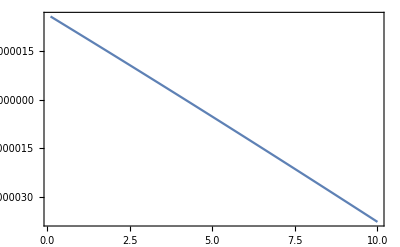
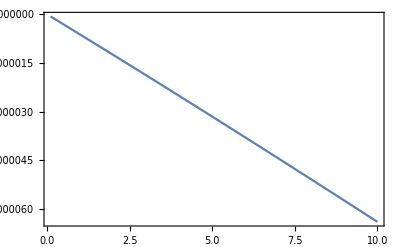
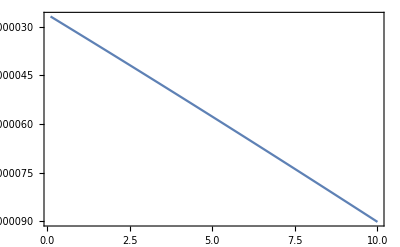
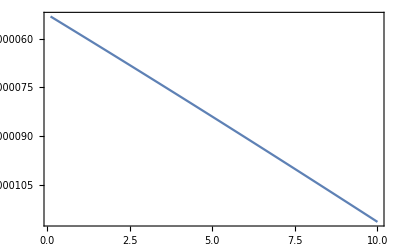

```mathematica
{Plot[EqnSpecX[xx/mee,1/5,-2],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,-1],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,0],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecX[xx/mee,1/5,1],{xx,1/10,10},Frame->True,PlotRange->Full]}(*хороший пик*)
```

```mathematica
FindRoot[EqnSpecX[xx/mee,1/5,-2],{xx,4}]
```

{xx→4.17512}

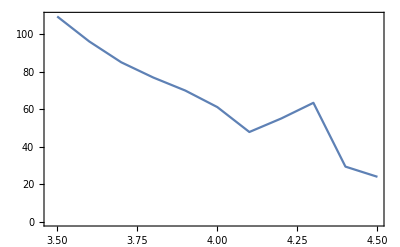
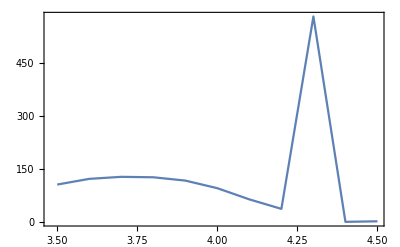

```mathematica
testp=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,3.5,4.5,0.1}];
testm=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,3.5,4.5,0.1}];
{ListLinePlot[testp,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[testm,Frame->True,Axes->False,PlotRange->Full]}
```

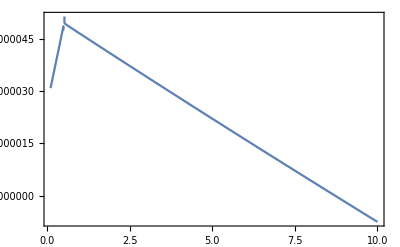
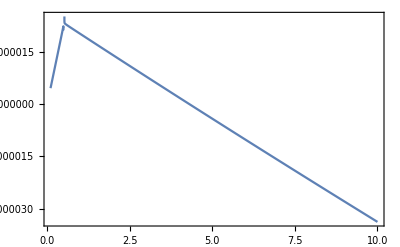
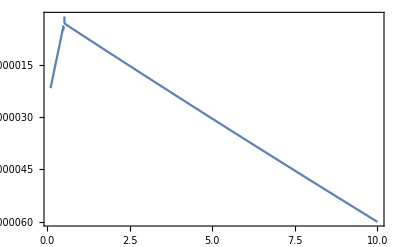
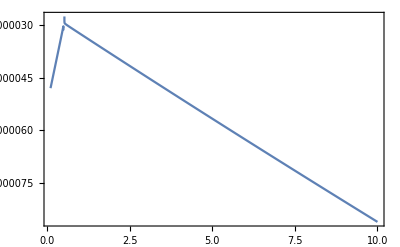

```mathematica
{Plot[EqnSpecY[xx/mee,1/5,-2],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,-1],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,0],{xx,1/10,10},Frame->True,PlotRange->Full],
Plot[EqnSpecY[xx/mee,1/5,1],{xx,1/10,10},Frame->True,PlotRange->Full]}(*пик только около 4х*)
```

```mathematica
FindRoot[EqnSpecY[xx/mee,1/5,-2],{xx,8}]
FindRoot[EqnSpecY[xx/mee,1/5,-1],{xx,4}]
```

{xx→8.71523}

{xx→4.29774}

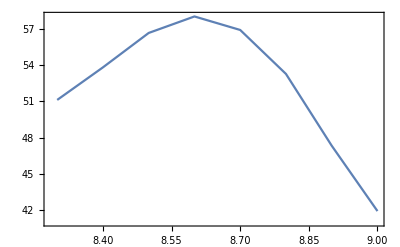
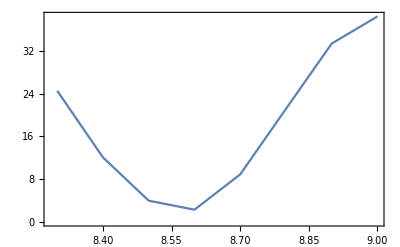

```mathematica
testp=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,8.3,9,0.1}];
testm=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,8.3,9,0.1}];
{ListLinePlot[testp,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[testm,Frame->True,Axes->False,PlotRange->Full]}
```

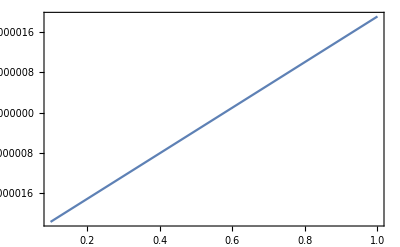
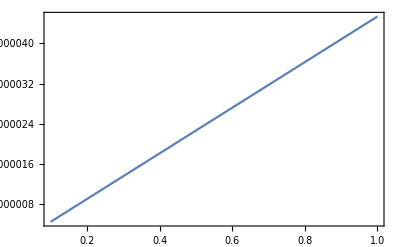
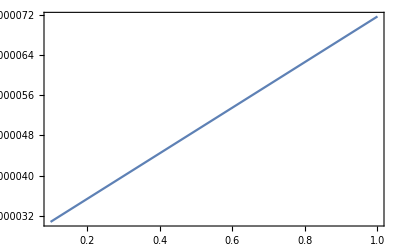
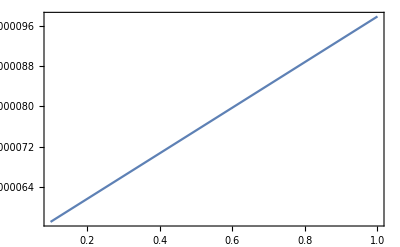

```mathematica
{Plot[EqnSpecTX[xx/mee,1/5,-2],{xx,1/10,1},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/5,-1],{xx,1/10,1},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/5,0],{xx,1/10,1},Frame->True,PlotRange->Full],
Plot[EqnSpecTX[xx/mee,1/5,1],{xx,1/10,1},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecTX[xx/mee,1/5,-2],{xx,1}](*вроде как пик*)
```

{xx→0.578856}

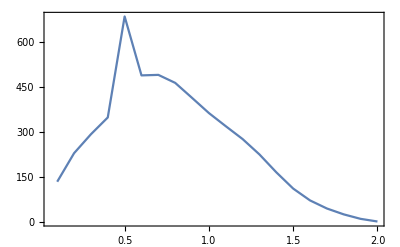
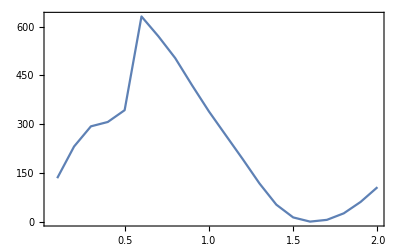

```mathematica
testp=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,0.1,2,0.1}];
testm=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,0.1,2,0.1}];
{ListLinePlot[testp,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[testm,Frame->True,Axes->False,PlotRange->Full]}
```

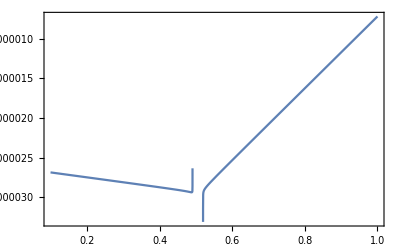
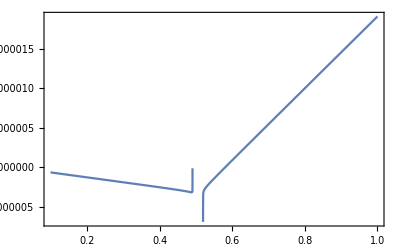
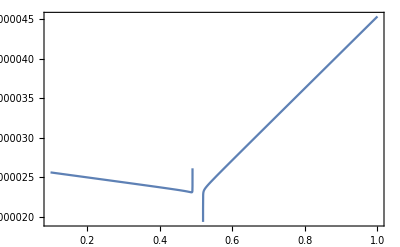
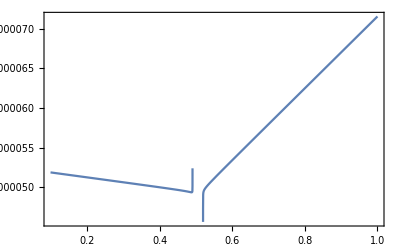

```mathematica
{Plot[EqnSpecTY[xx/mee,1/5,-2],{xx,1/10,1},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/5,-1],{xx,1/10,1},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/5,0],{xx,1/10,1},Frame->True,PlotRange->Full],
Plot[EqnSpecTY[xx/mee,1/5,1],{xx,1/10,1},Frame->True,PlotRange->Full]}
```

```mathematica
FindRoot[EqnSpecTY[xx/mee,1/5,-1],{xx,1}](*точка попадает в область предыдщего пика*)
```

{xx→0.580237}

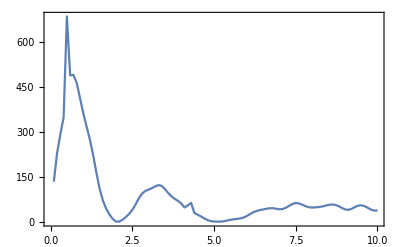
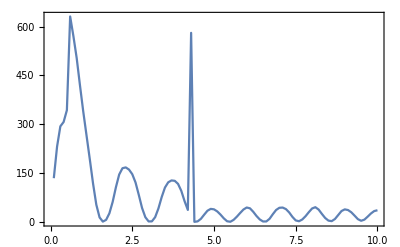

```mathematica
ploptp=ParallelTable[{x,dProbabPlane[1,x/mee,1/5,0]},{x,0.1,10,0.1}];
ploptm=ParallelTable[{x,dProbabPlane[-1,x/mee,1/5,0]},{x,0.1,10,0.1}];
{ListLinePlot[ploptp,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[ploptm,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*нужно построить более детальные графики в пиках*)
```

```mathematica
ll2ts1=AmplTwistTab[1,4.17512362437243/mee,4.17512362437243/mee/5];
ll2tsm1=AmplTwistTab[-1,4.17512362437243/mee,4.17512362437243/mee/5];
```

```mathematica
tm2s1=Table[{m,dProbabTwist[m,ll2ts1[[3]]]},{m,-mMax,mMax}];
tm2sm1=Table[{m,dProbabTwist[m,ll2tsm1[[3]]]},{m,-mMax,mMax}];
(*не очень хорошее распределение по m, l=-3?*)
```

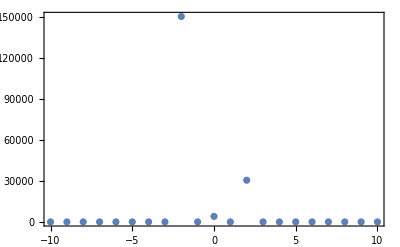
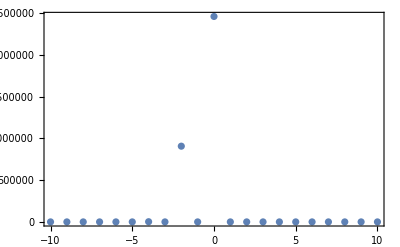

```mathematica
{ListPlot[tm2s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm2sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
ll3ts1=AmplTwistTab[1,4.297743995880004/mee,4.297743995880004/mee/5];
ll3tsm1=AmplTwistTab[-1,4.297743995880004/mee,4.297743995880004/mee/5];
```

```mathematica
tm3s1=Table[{m,dProbabTwist[m,ll3ts1[[3]]]},{m,-mMax,mMax}];
tm3sm1=Table[{m,dProbabTwist[m,ll3tsm1[[3]]]},{m,-mMax,mMax}];
(*[хорошее распределение по m, строим его*)
```

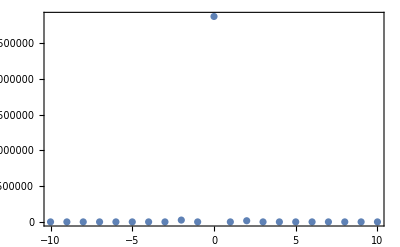
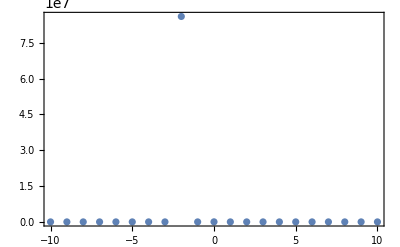

```mathematica
{ListPlot[tm3s1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tm3sm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
llts1=AmplTwistTab[1,0.5788556904766569/mee,0.5788556904766569/mee/5];
lltsm1=AmplTwistTab[-1,0.5788556904766569/mee,0.5788556904766569/mee/5];
```

```mathematica
tms1=Table[{m,dProbabTwist[m,llts1[[3]]]},{m,-mMax,mMax}];
tmsm1=Table[{m,dProbabTwist[m,lltsm1[[3]]]},{m,-mMax,mMax}];
(*тривиальное распределение по m*)
```

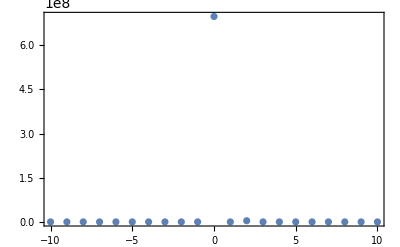
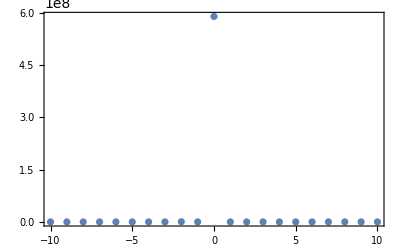

```mathematica
{ListPlot[tms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[tmsm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
l4s1=AmplTwistTab[1,0.5802368125180908/mee,0.5802368125180908/mee/5];
l4sm1=AmplTwistTab[-1,0.5802368125180908/mee,0.5802368125180908/mee/5];
```

```mathematica
t4ms1=Table[{m,dProbabTwist[m,l4s1[[3]]]},{m,-mMax,mMax}];
t4msm1=Table[{m,dProbabTwist[m,l4sm1[[3]]]},{m,-mMax,mMax}];
(*тривиальное распределение по m*)
```

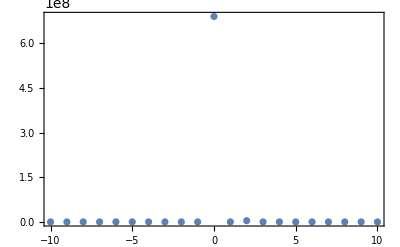
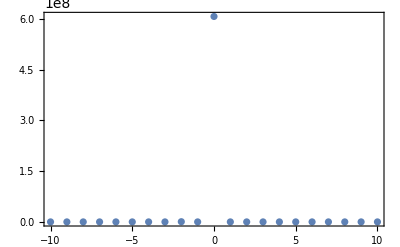

```mathematica
{ListPlot[t4ms1,Frame->True,Axes->False,PlotRange->Full],ListPlot[t4msm1,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*------гауссов пучок. нормальное падение-------*)
```

```mathematica
(*===================Задаем параметры амплитуды=====================*)
ss1=1;(*спиральность фотона*)
kom2=4.297743995880004/mee;(*энергия излучения*)
np11=SetPrecision[1/5,90];(*n_perp*)
(*NN1=20;(*диапазон ненулевых m*)*)
(*NNl=-15;
NNr=15;*)
sigpc=1/(kom2 np11);
Print["Критическое значение поперечного размера пучка: ",sigpc lc 10^4," мкм"]
"Критическое значение поперечного размера пучка: "0.11368645533141207" мкм"
```

Критическое значение поперечного размера пучка: 0.229476 мкм

Критическое значение поперечного размера пучка: 0.113686 мкм

```mathematica
Np=10^9/(10^4);(*число частиц в пучке*)
sig3=SetPrecision[0.015/lc,90];(*продольный размер. 0.5 ps*)
sigp=SetPrecision[1 10^(-4)/lc,90];(*поперечный размер. 1.25 мкм*)
β3=Sqrt[1-1/γ^2];(*скорость вдоль оси*)
ex=SetPrecision[0.9,90];(*эксцентриситет*)
hx=SetPrecision[0.1,90];(*смещение центра в долях sigp*)
hy=SetPrecision[0.05,90];(*смещение центра в долях sigp*)
ϵy=Sqrt[1-ex^2/2];
ϵx=Sqrt[(1-ex^2/2)/(1-ex^2)];
Print["Продольный размер пучка: ",sig3 lc 10^4," мкм"]
Print["Параметр продольной когерентности: ",kom2 sig3 Sqrt[1-np11^2]]
Print["Параметр размазанности по m: ",kom2 sigp np11]
```

Продольный размер пучка: 150. мкм

Параметр продольной когерентности: 3202.28

Параметр размазанности по m: 4.35775

```mathematica
(*===============Cчитаем амплитуду для разных n_perp и фиксированном kom======================*)
```

```mathematica
npmin=SetPrecision[np11/4,90];(*диапазон npp*)
npmax=SetPrecision[1.5 np11,90];(*диапазон npp*)
npst=10;(*число шагов*)
```

```mathematica
AmplBunchMNpp=Module[{npp2},
Table[{npp2,AmplTwistTab[ss1,kom2,kom2 npp2][[3]]},{npp2,npmin,npmax,(npmax-npmin)/npst}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Nnpnt=Length[AmplBunchMNpp[[1,2]]];(*число достоверных m*)
AmplBunchMNppf=Module[{mm,nnp,Nn},Nn=Nnpnt;Table[{{mm,nnp},I^(-mm) AmplBunchMNpp[[1+Round[npst (nnp-npmin)/(npmax-npmin)],2,1+Mod[mm,Nn]]]},{mm,-Floor[Nn/2],Floor[Nn/2]},{nnp,npmin,npmax,(npmax-npmin)/npst}]];
```

```mathematica
Put[AmplBunchMNppf,NotebookDirectory[]<>"ampl"<>"k0_"<>ToString[Round[kom2 mee]]<>"np_"<>ToString[Round[100 np11]]<>"s_"<>ToString[ss1+1]<>".dat"];(*записываем таблицу в файл*)
```

```mathematica
intAmpl0mnp=Interpolation[Flatten[AmplBunchMNppf,1]];(*строим функцию от (m,np)*)
NNl=-Min[2 mMax,Floor[Nnpnt/2]];NNr=-NNl;
iintAmpl0mnnp[xx_,yy_]:=If[xx>NNr||xx<NNl||yy>npmax||yy<npmin,0,intAmpl0mnp[xx,yy]];(*зануляем вне насчитанной области*)
```

```mathematica
alph[k_]:=If[k==0,1,(ⅇ^(ⅈ k Arg[hx/ϵx-ⅈ hy/ϵy])/(Abs[k]!)(hx^2/ϵx^2+hy^2/ϵy^2)^(Abs[k]/2)+If[EvenQ[k],1/(Abs[k/2]!)((ϵy^-2-ϵx^-2)/2)^Abs[k/2],0])/2^(Abs[k])](*коэффициенты ряда Фурье*)
```

```mathematica
ff1a=Module[{k},ParallelTable[Assuming[x>0,(2^-m x^(2 m-k))/(m!) HypergeometricPFQ[{m-k/2+1/2,m-k/2+1},{m+1,2m-k+1},-2 x^2]//FunctionExpand],{k,NNl-NNr-1,0}]];
ff1[m1_,k_,x1_]:=ff1a[[k-(NNl-NNr-1)+1]]/.{x->x1,m->m1};
ff1[50000,-10,SetPrecision[50000,80]]
ff2a=Module[{k},ParallelTable[Assuming[x>0,(2^(k-m)x^(2 m-k))/((m-k)!) HypergeometricPFQ[{m-k/2+1/2,m-k/2+1},{m-k+1,2m-k+1},-2 x^2]//FunctionExpand],{k,0,NNr-NNl+1}]];
ff2[m1_,k_,x1_]:=ff2a[[k+1]]/.{x->x1,m->m1};
ff2[50000,10,SetPrecision[50000,80]]
```

0.0058842747512157092306408

0.0058851806895738770502371

```mathematica
fg2Dp[m_,k_,x_]:=alph[k] If[k<=0,ff1[m,k,x],If[m≥k,ff2[m,k,x],(-1)^(m+k) k!x^k HypergeometricPFQRegularized[{(k+1)/2,(k+2)/2},{k-m+1,m+1},-2 x^2]]]
fg2D[m_,n_,x_]:=If[m≥0,fg2Dp[m,m-n,x],If[n>=0,Conjugate[fg2Dp[n,n-m,x]],(-1)^(m+n) fg2Dp[-n,m-n,x]]]
φg2D[m_,x_,y1_,nn3_,sg_]:=If[(y1/β3)^2 sg^2/2 +x^2/2 -Abs[m] Log[x]>30,0,Exp[-(y1/β3 )^2 sg^2/2]alph[m](-1)^((m-Abs[m])/2) x^Abs[m] Exp[-x^2/2]]
```

```mathematica
dPbnp[m_?IntegerQ,σ3_?NumberQ,RR_?NumberQ,Np1_?NumberQ,kom1_?NumberQ,nnp_?NumberQ]:=2 α/Pi Np1 Module[{n1,n2,ssu=0,aa},
Do[Do[aa=iintAmpl0mnnp[n1,nnp]Conjugate[iintAmpl0mnnp[n2,nnp]];ssu=ssu+If[Abs[aa]<10^(-30),0,
(fg2D[m-n1,m-n2,kom1 RR nnp]+(Np1-1) φg2D[m-n1,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3] Conjugate[φg2D[m-n2,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3]])aa],{n2,NNl,NNr}],{n1,NNl,NNr}];ssu](*вклады квадратов амплитуд, меньших 10^(-30), отбрасываются*)
```

```mathematica
dProbabTwist1np[mm_?IntegerQ,nnp_?NumberQ]:=2 α/Pi Abs[intAmpl0mnp[mm,nnp]]^2
```

```mathematica
(*===============Cчитаем амплитуду для разных k0 и фиксированном n_perp======================*)
```

```mathematica
komin=SetPrecision[kom2/4,90];(*диапазон ko*)
komax=SetPrecision[1.5 kom2,90];(*диапазон ko*)
kost=10;(*число шагов*)
```

```mathematica
AmplBunchMKo=Module[{koo},
Table[{koo,AmplTwistTab[ss1,koo,koo np11][[3]]},{koo,komin,komax,(komax-komin)/kost}]];(*таблица амплитуд по k0 при фиксированном nperp=np11*)
```

```mathematica
Nnpnt1=Length[AmplBunchMKo[[1,2]]];(*число достоверных m*)
AmplBunchMKof=Module[{mm,koo,Nn},Nn=Nnpnt1;Table[{{mm,koo},I^(-mm) AmplBunchMKo[[1+Round[kost (koo-komin)/(komax-komin)],2,1+Mod[mm,Nn]]]},{mm,-Floor[Nn/2],Floor[Nn/2]},{koo,komin,komax,(komax-komin)/kost}]];
```

```mathematica
Put[AmplBunchMKof,NotebookDirectory[]<>"ampl"<>"np_"<>ToString[Round[100 np11]]<>"ko_"<>ToString[Round[kom2 mee]]<>"s_"<>ToString[ss1+1]<>".dat"];(*записываем таблицу в файл*)
```

```mathematica
intAmpl0mko=Interpolation[Flatten[AmplBunchMKof,1]];(*строим функцию от (m,ko)*)
NNl1=-Min[2 mMax,Floor[Nnpnt1/2]];NNr1=-NNl1;
iintAmpl0mkoo[xx_,yy_]:=If[xx>NNr1||xx<NNl1||yy>komax||yy<komin,0,intAmpl0mko[xx,yy]];(*зануляем вне насчитанной области*)
```

```mathematica
dPbko[m_?IntegerQ,σ3_?NumberQ,RR_?NumberQ,Np1_?NumberQ,kom1_?NumberQ,nnp_?NumberQ]:=2 α/Pi Np1 Module[{n1,n2,ssu=0,aa},
Do[Do[aa=iintAmpl0mkoo[n1,kom1]Conjugate[iintAmpl0mkoo[n2,kom1]];ssu=ssu+If[Abs[aa]<10^(-30),0,
(fg2D[m-n1,m-n2,kom1 RR nnp]+(Np1-1) φg2D[m-n1,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3] Conjugate[φg2D[m-n2,kom1 RR nnp,kom1,Sqrt[1-nnp^2],σ3]])aa],{n2,NNl1,NNr1}],{n1,NNl1,NNr1}];ssu](*вклады квадратов амплитуд, меньших 10^(-30), отбрасываются*)
```

```mathematica
dProbabTwist1ko[mm_?IntegerQ,koo_?NumberQ]:=2 α/Pi Abs[intAmpl0mko[mm,koo]]^2
```

```mathematica
(*+++++++++++++++plots++++++++++++++++*)
```

```mathematica
(*\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\ПУЧОК s = 1*)
(*пучковые графикипо энергии s=1 np =1/5*)
bkos1mm2=ParallelTable[{x,Re[dPbko[-2,sig3,sigp,Np,x/mee,np11]]},{x,3,6,0.05}];
bkos1mm1=ParallelTable[{x,Re[dPbko[-1,sig3,sigp,Np,x/mee,np11]]},{x,3,6,0.05}];
bkos1m0=ParallelTable[{x,Re[dPbko[0,sig3,sigp,Np,x/mee,np11]]},{x,3,6,0.05}];
bkos1m1=ParallelTable[{x,Re[dPbko[1,sig3,sigp,Np,x/mee,np11]]},{x,3,6,0.05}];
bkos1m2=ParallelTable[{x,Re[dPbko[2,sig3,sigp,Np,x/mee,np11]]},{x,3,6,0.05}];

(*пучковые графикипо np s=1 ko =4.29*)
bnps1mm2=ParallelTable[{x,Re[dPbnp[-2,sig3,sigp,Np,kom2,x]]},{x,0,1,0.05}];
bnps1mm1=ParallelTable[{x,Re[dPbnp[-1,sig3,sigp,Np,kom2,x]]},{x,0,1,0.05}];
bnps1m0=ParallelTable[{x,Re[dPbnp[0,sig3,sigp,Np,kom2,x]]},{x,0,1,0.05}];
bnps1m1=ParallelTable[{x,Re[dPbnp[1,sig3,sigp,Np,kom2,x]]},{x,0,1,0.05}];
bnps1m2=ParallelTable[{x,Re[dPbnp[2,sig3,sigp,Np,kom2,x]]},{x,0,1,0.05}];
```

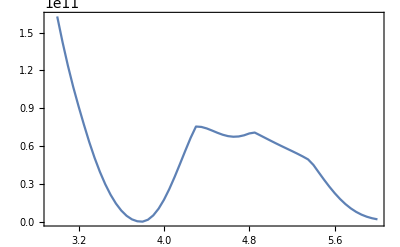
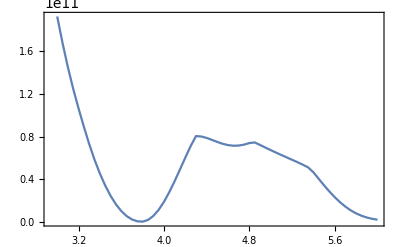
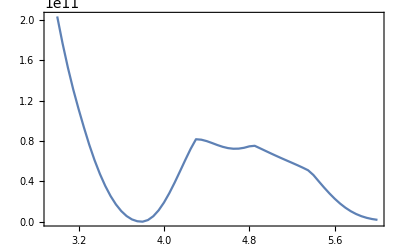
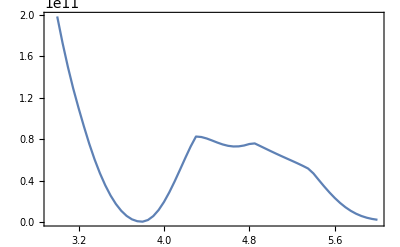
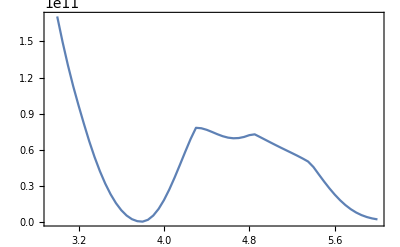

```mathematica
(*пучковые графикипо энергии s=1 np =1/5*)
{ListLinePlot[bkos1mm2,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkos1mm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkos1m0,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkos1m1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkos1m2,Frame->True,Axes->False,PlotRange->Full]}(*не очень хорошие графики,для s=1 ожидалось*)
```

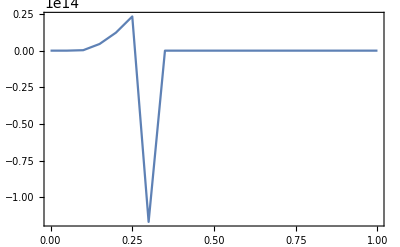
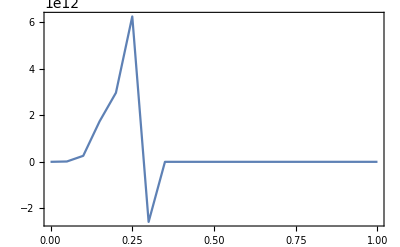
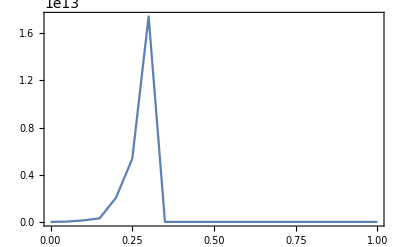
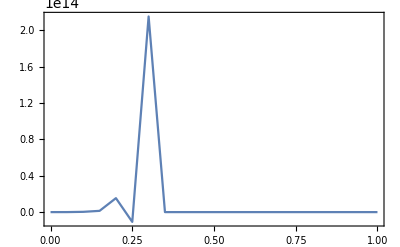
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*пучковые графикипо np s=1 ko =4.29*)
{ListLinePlot[bnps1mm2,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnps1mm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnps1m0,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnps1m1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnps1m2,Frame->True,Axes->False,PlotRange->Full]}
```

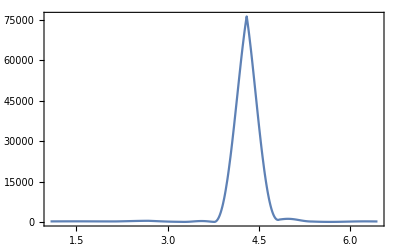
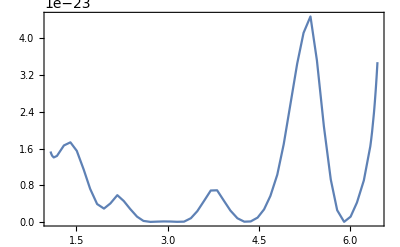
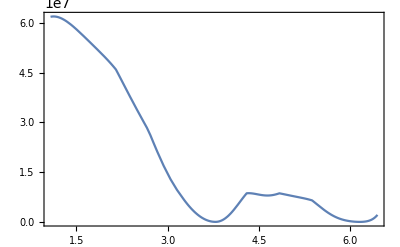
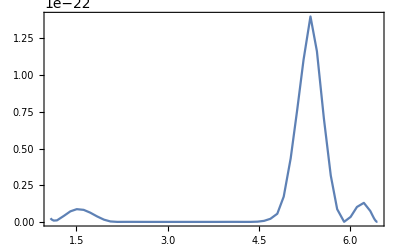
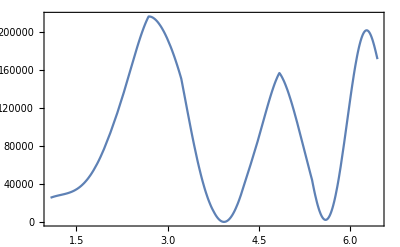

```mathematica
(*ОДНОЧАСТИЧНЫЕ ГРАФИКИ s=1*)
(*s=1,np=1/5,m=-2;-1;0;1;2*)
{Plot[dProbabTwist1ko[-2, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[-1, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full], 
Plot[dProbabTwist1ko[0, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[1, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[2, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full]}
(*есть хороший, но слабый пик m=-2*)
```

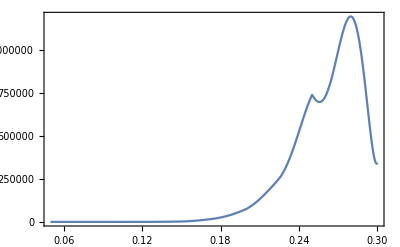
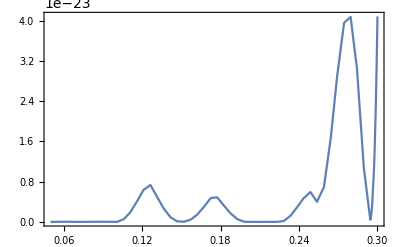
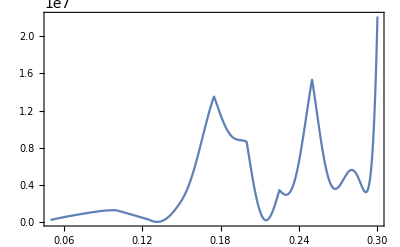
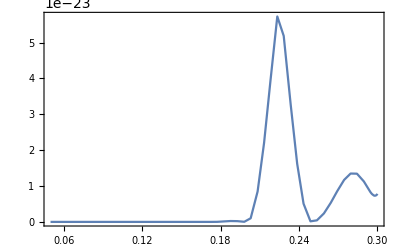
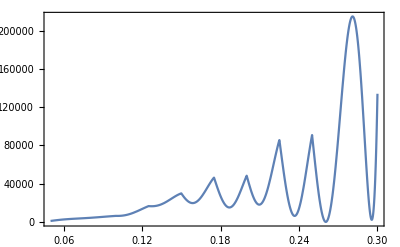

```mathematica
(*s=1,ko=4.29,m=-2;-1;0;1;2*)
{Plot[dProbabTwist1np[-2, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[-1, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[0, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[1, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[2, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*одначастичные графики по энергии выглядят лучше на пучковые, а графики по np наоборот, хм...*)
```

```mathematica
(*\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\\ПУЧОК s = -1*)
```

```mathematica
(*пучковые графикипо энергии s=-1 np =1/5*)
bkosm1mm2=ParallelTable[{x,Re[dPbko[-2,sig3,sigp,Np,x/mee,np11]]},{x,3,6,0.05}];
bkosm1mm1=ParallelTable[{x,Re[dPbko[-1,sig3,sigp,Np,x/mee,np11]]},{x,3,6,0.05}];
bkosm1m0=ParallelTable[{x,Re[dPbko[0,sig3,sigp,Np,x/mee,np11]]},{x,3,6,0.05}];
bkosm1m1=ParallelTable[{x,Re[dPbko[1,sig3,sigp,Np,x/mee,np11]]},{x,3,6,0.05}];
bkosm1m2=ParallelTable[{x,Re[dPbko[2,sig3,sigp,Np,x/mee,np11]]},{x,3,6,0.05}];

(*пучковые графикипо np s=1 ko =4.29*)
bnpsm1mm2=ParallelTable[{x,Re[dPbnp[-2,sig3,sigp,Np,kom2,x]]},{x,0,1,0.05}];
bnpsm1mm1=ParallelTable[{x,Re[dPbnp[-1,sig3,sigp,Np,kom2,x]]},{x,0,1,0.05}];
bnpsm1m0=ParallelTable[{x,Re[dPbnp[0,sig3,sigp,Np,kom2,x]]},{x,0,1,0.05}];
bnpsm1m1=ParallelTable[{x,Re[dPbnp[1,sig3,sigp,Np,kom2,x]]},{x,0,1,0.05}];
bnpsm1m2=ParallelTable[{x,Re[dPbnp[2,sig3,sigp,Np,kom2,x]]},{x,0,1,0.05}];
```

```mathematica
(*пучковые графикипо энергии s=1 np =1/5*)
{ListLinePlot[bkosm1mm2,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkosm1mm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkosm1m0,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkosm1m1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bkosm1m2,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*пучковые графикипо np s=1 ko =4.29*)
{ListLinePlot[bnpsm1mm2,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnpsm1mm1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnpsm1m0,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnpsm1m1,Frame->True,Axes->False,PlotRange->Full],ListLinePlot[bnpsm1m2,Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*ОДНОЧАСТИЧНЫЕ ГРАФИКИ s=-1*)
(*s=-1,np=1/5,m=-2;-1;0;1;2*)
{Plot[dProbabTwist1ko[-2, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[-1, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full], 
Plot[dProbabTwist1ko[0, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[1, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full],Plot[dProbabTwist1ko[2, x/mee],{x,komin*mee,komax*mee},Frame->True,Axes->False,PlotRange->Full]}
```

```mathematica
(*s=-1,ko=4.29,m=-2;-1;0;1;2*)
{Plot[dProbabTwist1np[-2, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[-1, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[0, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[1, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full],
Plot[dProbabTwist1np[2, x],{x,npmin,npmax},Frame->True,Axes->False,PlotRange->Full]}
```